```mathematica
Clear["Global`*"]
Assuming[q>0,Integrate[Integrate[(x-k)^2+(y-k)^2-(x^q+y^q)^(2/q),{x,0,k^2}],{y,0,k^2}]]
```

2/3 k^6 (3+(-3+k) k)-(2 k^4 (k^2)^(2 q) (2+q (4+q)))/((1+q)^2 (1+2 q))

```mathematica
Clear["Global`*"]
(* (x-1)^2 + (y-1)^2 = 1*)
circq[x_,y_,k_,q_]:=(x-k)^2+(y-k)^2
normq[x_,y_,q_]:=Abs[x]^q+Abs[y]^q

Manipulate[
pregion=RegionPlot[
normq[x,y,q]^(1/q)≤ k,
{x,-k,k},
{y,-k,k},
PlotLabel->"q = "<>ToString[N[q]]<>", k = "<>ToString[k],
PlotRange->{{-0.25,3},{-0.25,3}},
Frame->False,
Axes->Automatic,
BoundaryStyle->{Blue},
PlotStyle->{Blue,Opacity[0.2]},
Method->{"TransparentPolygonMesh"->True}];
pcirc=RegionPlot[
circq[x,y,k,q]^(1/2)≤k,
{x,-2k,2k},
{y,-2k,2k},
BoundaryStyle->{Green},
PlotStyle->{Green,Opacity[0.2]}
];

Show[pregion,pcirc],
{{q,1/2}, 0, 2},
{{k,1.5}, 0, 4, 0.05}]
```

```mathematica
Clear["Global`*"]
normq2d[x_,y_,q_]:=(x^q+y^q)^(1/q)

Manipulate[
pregion=RegionPlot[
normq2d[x,y,q]≤ k,
{x,0,k},
{y,0,k},
PlotLabel->"q = "<>ToString[N[q]]<>", k = "<>ToString[k],
PlotRange->{{0,k},{0,k}},
Frame->False,
Axes->Automatic,
BoundaryStyle->{Blue},
PlotStyle->{Blue,Opacity[0.2]},
Method->{"TransparentPolygonMesh"->True}];
pcirc=RegionPlot[
normq2d[x-k,y-k,2]≤k,
{x,0,2k},
{y,0,2k},
BoundaryStyle->{Green},
PlotStyle->{Green,Opacity[0.2]}
];

Show[pregion,pcirc],
{{q,0.562}, 0, 2},
{{k,1.5}, 0, 4, 0.05}]
```

```mathematica
Clear["Global`*"]
normq2d[x_,y_,q_]:=(x^q+y^q)^(1/q)

Manipulate[
pregion=RegionPlot[
normq2d[x,y,q]≤ k,
{x,0,k},
{y,0,k},
PlotLabel->"q = "<>ToString[N[q]]<>", k = "<>ToString[k],
PlotRange->{{-0.25,3},{-0.25,3}},
Frame->False,
Axes->Automatic,
BoundaryStyle->{Blue},
PlotStyle->{Blue,Opacity[0.2]},
Method->{"TransparentPolygonMesh"->True}];
pcirc=RegionPlot[
normq2d[x-k,y-k,2]≤ k,
{x,0,2k},
{y,0,2k},
BoundaryStyle->{Green},
PlotStyle->{Green,Opacity[0.2]}
];
p3=RegionPlot[
 normq2d[x,y,q]-normq2d[x-k,y-k,2]≥0,
{x,0,k},
{y,0,k},
PlotLabel->"q = "<>ToString[N[q]]<>", k = "<>ToString[k],
PlotRange->{{-0.25,3},{-0.25,3}},
Frame->False,
Axes->Automatic,
BoundaryStyle->{Red},
PlotStyle->{Red,Opacity[0.2]},
Method->{"TransparentPolygonMesh"->True}];

Show[pregion,pcirc,p3],
{{q,1/2}, 0, 2},
{{k,1.5}, 0, 4, 0.05}]
```

```mathematica
Clear["Global`*"]
f1[x_,k_,q_]:=(k^q-x^q)^(1/q)
f2[x_,k_,q_]:=-(k^2-(x-k)^2)^(1/2)+k

(*
Manipulate[
Plot[{
1/k^2(f2[x,k,2]-f1[x,k,q])^2},
{x,0,k},
PlotRange->{0,0.025},
PlotLabel->"q = "<>ToString[N[q]]<>", k = "<>ToString[k],
AxesLabel->Automatic],
{{q,1/2}, 0, 2},
{{k,1.5}, 0, 4, 0.05}]
*)
k=1;
f[q_]:=NIntegrate[1/k^2(f2[x,k,2]-f1[x,k,q])^2,{x,0,k}]
NMinimize[{f[q],q>0&&q<1},q,WorkingPrecision->100,AccuracyGoal->100]
```

NIntegrate::inumr: The integrand (1-√(1-Plus[«2»]^2)-(1-x^q)^(1/q))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{8.12151462679691526678170399033973581026657484471797943115234375×10^-6,{q→0.5621464103501893229543725289214607886065249327294934138883361734532867995395071443900958907857819854}}

```mathematica
f[0.562146]
```

8.12151×10^-6

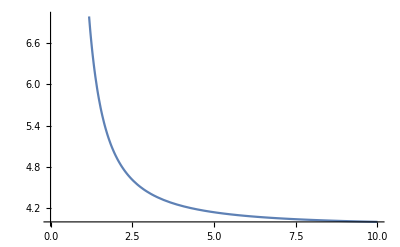

```mathematica
Clear["Global`*"]
normq2d[x_,y_,q_]:=(x^q+y^q)^(1/q)
k=2;
f[q_]:=NIntegrate[(normq2d[x,y,q]-normq2d[x-k,y-k,2])^2,{x,0,k},{y,0,k}]

Plot[f[q],{q,0,10}]
```

```mathematica
Clear["Global`*"]
q=0.562;
fobj[x_,y_,a_,b_]:=-(a x + b y)+1/2 (x^2+y^2)
gconstr1[x_,y_,q_]:=x^q+y^q
gconstr2[x_,y_,k_]:=gconstr1[x-k,y-k,2]

a=0.8;
b=0.9;

Manipulate[
pobj=ContourPlot[
fobj[x,y,a,b],
{x,0,k},
{y,0,k},
PlotLabel->"k = "<>ToString[k]<>", q = "<>ToString[N[q]],
Contours->20,
ContourStyle->Thick,
(*ColorFunction->"BlueGreenYellow",*)
ContourShading->None,
Frame->False,
Axes->Automatic,
AxesLabel->Automatic,
Method->{"TransparentPolygonMesh"->True},
Epilog->{
PointSize[0.03], Red, Point[{a,b}],
PointSize[0.03], Blue, Point[{0.10557,0.55278}],
PointSize[0.03], Green, Point[{0.08446,0.5974}]
}
];
pconstr1=RegionPlot[
gconstr1[x,y,q]≤ k^q,
{x,0,k},
{y,0,k},
BoundaryStyle->{Green},
PlotStyle->{Green,Opacity[0.2]}
];
pconstr2=RegionPlot[
gconstr2[x,y,k]≤ k^2,
{x,0,k},
{y,0,k},
BoundaryStyle->{Blue},
PlotStyle->{Blue,Opacity[0.2]}
];
ptest=Plot[(k-x^q)^(1/q),{x,0,k},PlotStyle->Red];
Show[pobj,pconstr1,pconstr2,ptest],
{{k,1},0,3}
]
```

```mathematica
Clear["Global`*"]
a=0.8;
b=0.9;
k=1;
q=0.5621464103501893;
ArgMax[{-(-(a x + b y)+1/2(x^2+y^2)),x≥0&&y≥0&&x≤a&&y≤b&&((x-k)^2+(y-k)^2== k^2)},{x,y}]
ArgMin[{-(a x + b y)+1/2(x^2+y^2),x≥0&&y≥0&&x≤a&&y≤b&&(x^q+y^q==k)},{x,y}]
```

{0.105572,0.552787}

{0.089848,0.588032}

```mathematica
gradf[x_,y_]:={x-a,y-b}
g[x_,y_]:=x^q+y^q
gradg[X_,Y_]:= (Grad[g[x,y],{x,y}])/.{x->X,y->Y}
Solve[gradf[x,y]==λ gradg[x,y],{x,y}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[{-a+x,-b+y}=={(0.562 λ)/x^0.438,(0.562 λ)/y^0.438},{x,y}]

```mathematica
xmax=10;
Manipulate[
Plot[
(x+λ k)/(1 + 2λ),
{x,0,xmax},
PlotRange->{0,4},
PlotLabel->"λ = "<>ToString[λ]<>", k = "<>ToString[k]],
{{λ,0},0,10},
{{k,1},0,10}]
```

Plot::plln: Limiting value xmax in {x,0,xmax} is not a machine-sized real number.

```mathematica
Clear[x,y,k,a,b]
Solve[k^2==(x-k)^2+(y-k)^2,k]
```

{{k→x-√2 √x √y+y},{k→x+√2 √x √y+y}}

```mathematica
Clear[x,y,k,a,b]
sol=Solve[{
x==(a-2λ*(x+Sqrt[2x y] + y))/(1-2λ),
y==(b-2λ*(x+Sqrt[2x y] + y))/(1-2λ)},{x,y}];
sol1x[A_,B_,l_]:=(x/.sol[[1]])/.{a->A,b->B,λ->l}
sol1y[A_,B_,l_]:=(y/.sol[[1]])/.{a->A,b->B,λ->l}

sol2x[A_,B_,l_]:=(x/.sol[[2]])/.{a->A,b->B,λ->l}
sol2y[A_,B_,l_]:=(y/.sol[[2]])/.{a->A,b->B,λ->l}

Simplify[sol2x[a,b,l]]
Simplify[sol2y[a,b,l]]
a=0.9;
b=0.95;
```

(-2 b l+2 √2 (-1+2 l) √((l^2 (a b+2 a^2 (-1+l) l+2 b^2 (-1+l) l))/(1-2 l)^2)+a (1+2 l-4 l^2))/(1+2 l-12 l^2+8 l^3)

(-2 a l+2 √2 (-1+2 l) √((l^2 (a b+2 a^2 (-1+l) l+2 b^2 (-1+l) l))/(1-2 l)^2)+b (1+2 l-4 l^2))/(1+2 l-12 l^2+8 l^3)

```mathematica
Clear[x,y,k,a,b]
Solve[{x==(a-2λ ( x+Sqrt[2 x y] + y))/(1-2 λ),y==(b-2λ ( x+Sqrt[2 x y] + y))/(1-2 λ)},{x,y}]
```

{{x→1/(2 (-1-4 λ+4 λ^2))(-2 b-(2 a)/(1-2 λ)+(2 b)/(1-2 λ)-4 a λ-√((2 b+(2 a)/(1-2 λ)-(2 b)/(1-2 λ)+4 a λ)^2-4 (-b^2-a^2/(1-2 λ)^2+(2 a b)/(1-2 λ)^2-b^2/(1-2 λ)^2-(2 a b)/(1-2 λ)+(2 b^2)/(1-2 λ)) (-1-4 λ+4 λ^2))),y→-a/(1-2 λ)+b/(1-2 λ)-b/(-1-4 λ+4 λ^2)-a/((1-2 λ) (-1-4 λ+4 λ^2))+b/((1-2 λ) (-1-4 λ+4 λ^2))-(2 a λ)/(-1-4 λ+4 λ^2)-(√((2 b+(2 a)/(1-2 λ)-(2 b)/(1-2 λ)+4 a λ)^2-4 (-b^2-a^2/(1-2 λ)^2+(2 a b)/(1-2 λ)^2-b^2/(1-2 λ)^2-(2 a b)/(1-2 λ)+(2 b^2)/(1-2 λ)) (-1-4 λ+4 λ^2)))/(2 (-1-4 λ+4 λ^2))},{x→1/(2 (-1-4 λ+4 λ^2))(-2 b-(2 a)/(1-2 λ)+(2 b)/(1-2 λ)-4 a λ+√((2 b+(2 a)/(1-2 λ)-(2 b)/(1-2 λ)+4 a λ)^2-4 (-b^2-a^2/(1-2 λ)^2+(2 a b)/(1-2 λ)^2-b^2/(1-2 λ)^2-(2 a b)/(1-2 λ)+(2 b^2)/(1-2 λ)) (-1-4 λ+4 λ^2))),y→-a/(1-2 λ)+b/(1-2 λ)-b/(-1-4 λ+4 λ^2)-a/((1-2 λ) (-1-4 λ+4 λ^2))+b/((1-2 λ) (-1-4 λ+4 λ^2))-(2 a λ)/(-1-4 λ+4 λ^2)+(√((2 b+(2 a)/(1-2 λ)-(2 b)/(1-2 λ)+4 a λ)^2-4 (-b^2-a^2/(1-2 λ)^2+(2 a b)/(1-2 λ)^2-b^2/(1-2 λ)^2-(2 a b)/(1-2 λ)+(2 b^2)/(1-2 λ)) (-1-4 λ+4 λ^2)))/(2 (-1-4 λ+4 λ^2))}}

```mathematica
Clear[x,y,k,a,b]
Solve[k^2==x^2+y^2-2k(x+y)+2k^2,k]
```

{{k→x-√2 √x √y+y},{k→x+√2 √x √y+y}}

True